```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* 
1 - коллокация в точке;
2 - коллокация в подобластях;
3 - метод Бубнова - Галеркина;
4 - метод Галеркина;
5 - МНК; 
6 - метод Ритца;
*)
nM =6; (* номер метода *)
p = 3; (* порядок *)
```

## Исходные данные

```mathematica
leftBond=0;
rightBond=1;
A[ϕ_,x_]:=D[ϕ,{x,2}]+ϕ;
F[x_]:=-x;
ϕi[x_,i_]:=x^i-x^(i+1);
```

## Функции

```mathematica
projectionMethod[methodNumber_,order_]:=Module[{a,u,ψ,eq,eqRight,solA,numSol},
a=Table[Subscript[aa, i],{i,1,order}];

u=a.Table[ϕi[x,i],{i,1,order}];
Switch[methodNumber,
1,ψ=Table[DiracDelta[x-(leftBond + i (rightBond-leftBond)/(order+1))],{i,1,order}],
2,ψ=Table[If[leftBond+(i-1)(rightBond-leftBond)/order≤x<leftBond+i(rightBond-leftBond)/order,1,0],{i,1,order}],
3,ψ=Table[ϕi[x,i],{i,1,order}],
4,ψ=Table[(x-1/2)^(i-1),{i,1,order}],
5,ψ=Table[A[ϕi[x,i],x],{i,1,order}],
6,ψ=Table[D[u,Subscript[aa, i]],{i,1,order}]
];
eq=Table[∑_(i=1)^order a⟦i⟧∫_leftBond^rightBond A[ϕi[x,i],x]ψ⟦j⟧ⅆx,{j,1,order}];
eqRight=Table[∫_leftBond^rightBond F[x]ψ⟦j⟧ⅆx,{j,1,order}];
solA=Solve[eq==eqRight,a]⟦1⟧;
numSol[x_]:=∑_(i=1)^order a⟦i⟧ϕi[x,i]/.solA;
{a/.solA,numSol[x]}
]
```

```mathematica
makePrint[methodNumber_,quantity_]:=Module[{analyticalSol,i,a,numSol,δ,tableFraction,tableNum,tableErr,plot,name},
analyticalSol[x]:=DSolve[{A[u[ξ],ξ]==F[ξ],u[leftBond]==0,u[rightBond]==0},u[ξ],ξ]⟦1,1,2⟧/.ξ->x;
result={};
For[i=1,i≤quantity,i++,
{a,numSol[x]}=projectionMethod[methodNumber,i];
δ=√(Integrate[(analyticalSol[x]-numSol[x])^2,{x,leftBond,rightBond}]/Integrate[(analyticalSol[x])^2,{x,leftBond,rightBond}])//N;
result=Append[result,{a,numSol[x],δ}];
];
(*solsForPlot=Append[result⟦;;,2⟧,analyticalSol[x]];*)
solsForPlot=result⟦1;;Min[3,Length[result]],2⟧;
Print[result⟦;;,2⟧];
solsForPlot=Append[solsForPlot,analyticalSol[x]];
tableFraction = Grid[Prepend[Transpose@{Table[i,{i,1,quantity}],result⟦;;,1⟧},{"N","a_i"}],Frame->All];
tableNum =Grid[Prepend[Transpose@{Table[i,{i,1,quantity}],N[result⟦;;,1⟧]},{"N","a_i//N"}],Frame->All];
tableErr=Grid[Prepend[Transpose@{Table[i,{i,1,quantity}],result⟦;;,3⟧},{"N","δ"}],Frame->All];
plot=Plot[solsForPlot,{x,leftBond,rightBond},PlotLegends->Append[Table["numSol, N = "<>ToString[i],{i,1,Min[quantity,3]}],"analyticalSol"],AxesStyle->Black,LabelStyle->{13,Black},AxesLabel->{"x","u(x)"},PlotRange->All, ImageSize->1000, PlotStyle->{Red, Blue, Green, {Black, Dashed}}];
Print[tableFraction];
Print[tableNum];
Print[tableErr];
Print[plot];
]
```

## Печать результатов

{5/18 (x-x^2),71/369 (x-x^2)+7/41 (x^2-x^3),(13811 (x-x^2))/73554+(2380 (x^2-x^3))/12259-7/299 (x^3-x^4)}

N | a_i
1 | {5/18}
2 | {71/369,7/41}
3 | {13811/73554,2380/12259,-7/299}

N | a_i//N
1 | {0.277778}
2 | {0.192412,0.170732}
3 | {0.187767,0.194143,-0.0234114}

N | δ
1 | 0.115426
2 | 0.00371191
3 | 0.000324226

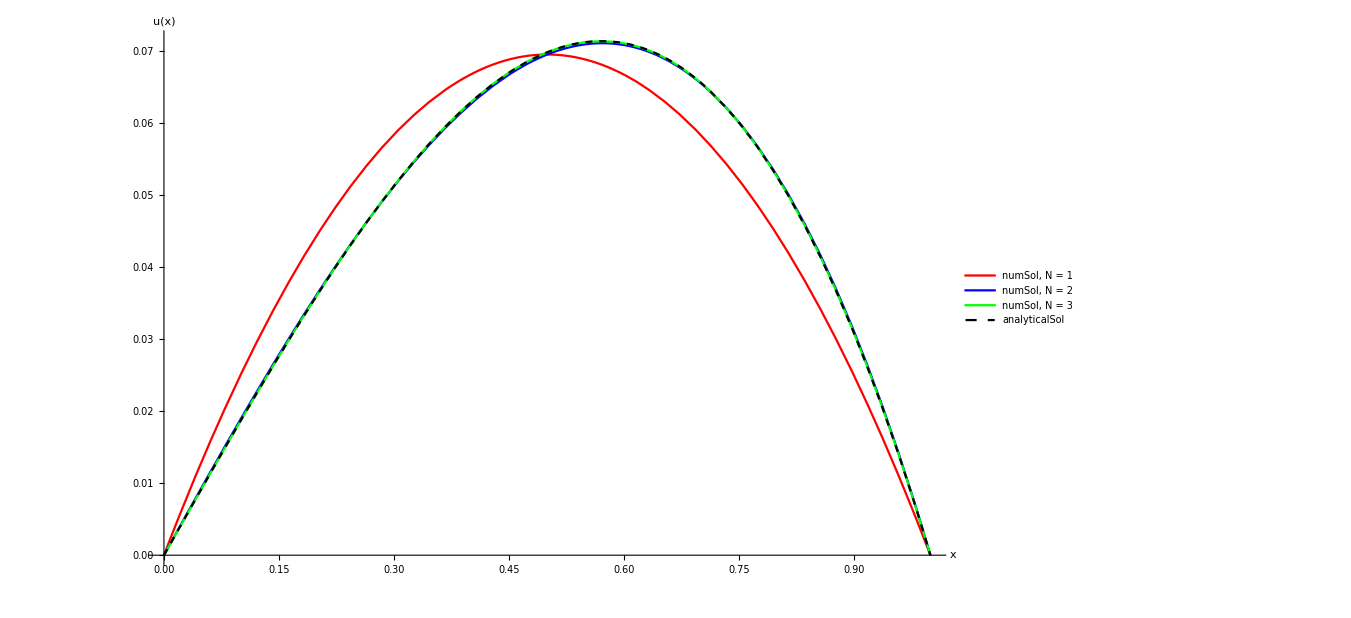

```mathematica
makePrint[nM,p]
```